```mathematica
Roots[x(x-1)==0,x]
```

x==1||x==0

```mathematica
Roots[Exp[I*x](x)==0,x]
```

Roots::neq: ⅇ^(ⅈ x) x is expected to be a polynomial in the variable x.

Roots[ⅇ^(ⅈ x) x==0,x]

```mathematica
Exp[0]
```

1

```mathematica
Exp[I*0]
```

1

```mathematica
Exp[I*5]
```

ⅇ^(5 ⅈ)

```mathematica
N[ⅇ^(5 ⅈ)]
```

0.283662-0.958924 ⅈ

```mathematica
Roots[-wn^2+2g*wn*I+w^2==0,wn]
```

wn==ⅈ g-√(-g^2+w^2)||wn==ⅈ g+√(-g^2+w^2)

```mathematica
C1*Exp[I*g+Sqrt[g&2+]]
```

```mathematica
Solve[-wn^2+2g*wn*I+w^2==0,wn]//Simplify
```

{{wn→ⅈ g-√(-g^2+w^2)},{wn→ⅈ g+√(-g^2+w^2)}}

```mathematica
C1=1
C2=1
k=6
g=0.8
```

1

1

6

0.8

```mathematica
t=5
```

5

```mathematica
1
```

1

```mathematica
Exp[-I*t]//Abs
```

1

```mathematica
A*Exp[-I*w*T]+B*Exp[I*w*T]//ExpToTrig//Simplify
```

(A+B) Cos[T w]-ⅈ (A-B) Sin[T w]

```mathematica
Refine[A*Exp[-I*w*T]+B*Exp[I*w*T],Element[A,Reals]]
```

A ⅇ^(-ⅈ T w)+B ⅇ^(ⅈ T w)

```mathematica
Cos[T w]-ⅈ Re[Sin[T w]]//Re
```

Re[Cos[T w]]

```mathematica
Re[x+I*Re[y]]
```

Re[x]

```mathematica
ExpToTrig[Re[ⅇ^(-5 ⅈ w)]]
```

Im[Sin[5 w]]+Re[Cos[5 w]]

```mathematica
Re[Exp[I*w*t]]//ExpToTrig
```

-Im[Sin[5 w]]+Re[Cos[5 w]]

```mathematica
Refine[
Re[Exp[I*Ω*T]],
{Element[T,Reals],Element[Ω,Reals]}]
```

Re[ⅇ^(ⅈ T Ω)]

```mathematica
Exp[I*Ω*T]//ExpToTrig
```

Cos[T Ω]+ⅈ Sin[T Ω]

```mathematica
Refine[
Re[Cos[T Ω]+ⅈ Sin[T Ω]],
{Element[T,Reals],Element[Ω,Reals]}]
```

Cos[T Ω]

```mathematica
(A1+I*B1)Exp[-I*Ω*T]//ExpToTrig//Expand
```

A1 Cos[T Ω]+ⅈ B1 Cos[T Ω]-ⅈ A1 Sin[T Ω]+B1 Sin[T Ω]

```mathematica
(A1+I*B1)Exp[-I*Ω*T]+(A2+I*B2)Exp[+I*Ω*T]//ExpToTrig//Expand
```

A1 Cos[T Ω]+A2 Cos[T Ω]+ⅈ B1 Cos[T Ω]+ⅈ B2 Cos[T Ω]-ⅈ A1 Sin[T Ω]+ⅈ A2 Sin[T Ω]+B1 Sin[T Ω]-B2 Sin[T Ω]

```mathematica
A*Exp[I*x]+B*Exp[-I*x]//ExpToTrig
```

A Cos[x]+B Cos[x]+ⅈ A Sin[x]-ⅈ B Sin[x]

```mathematica
Refine[Re[A Cos[x]+B Cos[x]+ⅈ A Sin[x]-ⅈ B Sin[x]],{Element[A,Reals],Element[B,Reals],Element[x,Reals]}]
```

A Cos[x]+B Cos[x]

```mathematica
FullSimplify[A Cos[x]+B Cos[x]+ⅈ A Sin[x]-ⅈ B Sin[x]]
```

(A+B) Cos[x]+ⅈ (A-B) Sin[x]

```mathematica
Exp[-g*t] (C1 Exp[ⅈ t √(k^2-g^2)]+C2 Exp[-ⅈ t √(k^2-g^2)])//Re
```

2 Re[ⅇ^-t]

```mathematica
(A1 Exp[ⅈ t √(κ^2-γ^2)]+B1 Exp[-ⅈ t √(κ^2-γ^2)])
```

B1 ⅇ^(-ⅈ t √(-γ^2+κ^2))+A1 ⅇ^(ⅈ t √(-γ^2+κ^2))

```mathematica
Simplify[B1 ⅇ^(-ⅈ t √(-γ^2+κ^2))+A1 ⅇ^(ⅈ t √(-γ^2+κ^2))]
```

```mathematica
ⅇ^(-ⅈ t √(-γ^2+κ^2)) (B1+A1 ⅇ^(2 ⅈ t √(-γ^2+κ^2)))//ExpToTrig
```

```mathematica
(Cos[t √(-γ^2+κ^2)]-ⅈ Sin[t √(-γ^2+κ^2)]) (B1+A1 Cos[2 t √(-γ^2+κ^2)]+ⅈ A1 Sin[2 t √(-γ^2+κ^2)])//Simplify
```

```mathematica
(A1+B1) Cos[t √(-γ^2+κ^2)]+ⅈ (A1-B1) Sin[t √(-γ^2+κ^2)]
```

(A1+B1) Cos[t √(-γ^2+κ^2)]+ⅈ (A1-B1) Sin[t √(-γ^2+κ^2)]

```mathematica
A1 Cos[t √(-γ^2+κ^2)]+B1 Cos[t √(-γ^2+κ^2)]+ⅈ A1 Sin[t √(-γ^2+κ^2)]-ⅈ B1 Sin[t √(-γ^2+κ^2)]
```

A1 Cos[t √(-γ^2+κ^2)]+B1 Cos[t √(-γ^2+κ^2)]+ⅈ A1 Sin[t √(-γ^2+κ^2)]-ⅈ B1 Sin[t √(-γ^2+κ^2)]

```mathematica
Manipulate[Plot[2 Cos[t √(-γ^2+κ^2)] (Cosh[t γ]-Sinh[t γ]),{t,-8,8}],{γ,-8,8},{κ,-2,2}]
```

```mathematica
ExpToTrig[Real[ⅇ^(-t γ) (ⅇ^(-ⅈ t √(-γ^2+κ^2))+ⅇ^(ⅈ t √(-γ^2+κ^2)))]]
```

Real[ⅇ^(-t γ) (ⅇ^(-ⅈ t √(-γ^2+κ^2))+ⅇ^(ⅈ t √(-γ^2+κ^2)))]

```mathematica
Simplify[Real[ⅇ^(-t γ) (ⅇ^(-ⅈ t √(-γ^2+κ^2))+ⅇ^(ⅈ t √(-γ^2+κ^2)))]]
```

Real[ⅇ^(-t γ-ⅈ t √(-γ^2+κ^2)) (1+ⅇ^(2 ⅈ t √(-γ^2+κ^2)))]

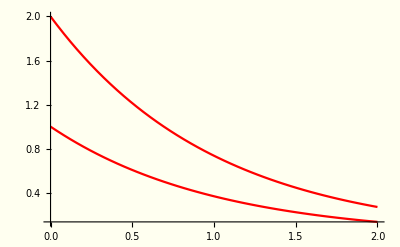

```mathematica
Plot[{Exp[-g*t],Exp[-g*t] (C1 Exp[ⅈ t √(k^2-g^2)]+C2 Exp[-ⅈ t √(k^2-g^2)])},{t,0,2},PlotTheme->"Minimal",Background->RGBColor[1.,1.,0.94117],PlotStyle->{Red},PlotRange->Full]
```

```mathematica
ClearAll[t]
```

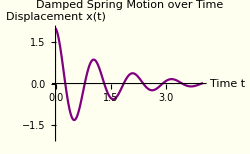

```mathematica
Show[%267,AxesLabel->{HoldForm[Time t],HoldForm[Displacement x[t]]},PlotLabel->HoldForm[Damped Spring Motion over Time],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%273,Axes->False]
```

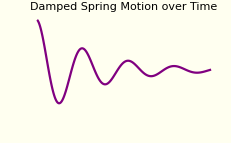

```mathematica
Show[%268,Axes->False]
```

```mathematica
Show[%67,Background->RGBColor[255,255,240]]
```

```mathematica
Show[%64,AxesLabel->{HoldForm[Time t],HoldForm[Displacement from Equillibrium (x t)]},PlotLabel->HoldForm[Damped Motion over Time (x t)],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%65,Axes->False]
```

```mathematica
Plot[{Exp[-γ*t],Exp[-γ*t]*(A*Cos[ω*t]+B*Sin[ω*t])},{t,0,1.5},PlotRange->{-0.7,1.15},PlotStyle->{{Dashed,Red},Purple},Background->RGBColor[1.,1.,0.94],
PlotLegends->{Exp[-γt],x[t]},PlotLabel->"x(t), Nonzero A,B"]
```

```mathematica
γ=9
k=2
ω=Sqrt[k^2-γ^2]
A=1
B=1
```

9

2

ⅈ √77

1

1

```mathematica
g=3.9
```

3.9

```mathematica
A=1
B=1
```

1

1

```mathematica
Needs[PlotLegend]
```

Needs::cxru: Context or appropriately structured rule expected at position 1 in Needs[PlotLegend].

Needs[PlotLegend]

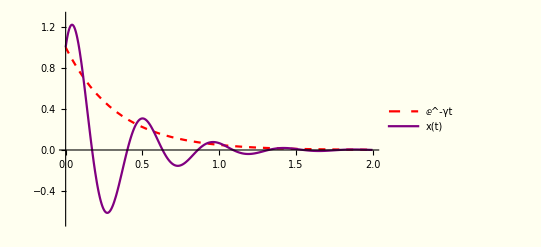

```mathematica
Plot[{Exp[-γ*t],Exp[-γ*t]*(A*Cos[ω*t]+B*Sin[ω*t])},{t,0,2},PlotRange->{-0.7,1.3},PlotStyle->{{Dashed,Red},Purple},Background->RGBColor[1.,1.,0.94],
PlotLegends->{Exp[-γt],x[t]}]
```

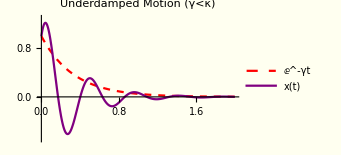

```mathematica
Show[%446,PlotLabel->HoldForm[Underdamped Motion (γ<κ)],LabelStyle->{GrayLevel[0]}]
```

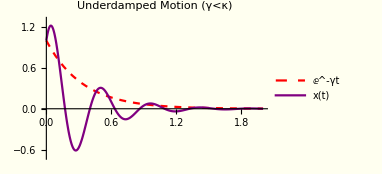

```mathematica
Show[%447,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.34]]]
```

```mathematica
k=1
g=1.8
```

1

1.8

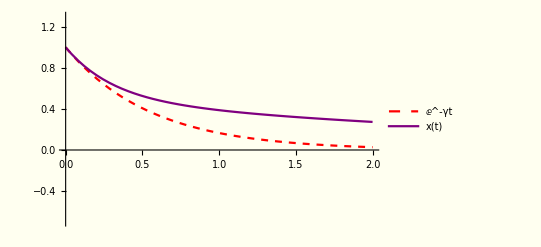

```mathematica
Plot[{Exp[-g*t],Exp[-g*t]*((1/2)Exp[ⅈ t √(k^2-g^2)]+(1/2)Exp[-ⅈ t √(k^2-g^2)])},{t,0,2},PlotRange->{-0.7,1.3},PlotStyle->{{Dashed,Red},Purple},Background->RGBColor[1.,1.,0.94],
PlotLegends->{Exp[-γt],x[t]}]
```

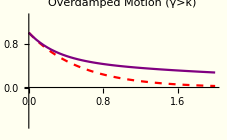

```mathematica
Show[%788,PlotLabel->HoldForm[Overdamped Motion (γ>κ)],LabelStyle->{GrayLevel[0]}]
```

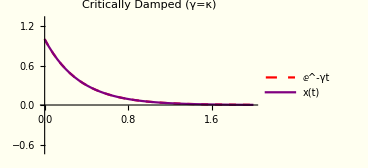

```mathematica
Show[%455,PlotLabel->HoldForm[Critically Damped (γ=κ)],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Plot[{Exp[-γ*t],(A*Cos[ω*t]+B*Sin[ω*t])},{t,0,2},PlotRange->{-2,2},PlotStyle->{{Dashed,Red},Purple}]
```

-Graphics-

```mathematica
t=0
```

0

```mathematica
Exp[-γ*t]*(A*Cos[ω*t]+B*Sin[ω*t])
```

1

```mathematica
ClearAll[t]
```

```mathematica
Exp[-γ*t]
```

1

```mathematica
(A*Cos[ω*t]+B*Sin[ω*t])
```

1

```mathematica
F1*Exp[I*Sqrt[wo^2-G^2]]+F2*Exp[-I*Sqrt[wo^2-G^2]]
```

ⅇ^(ⅈ √(-G^2+wo^2)) F1+ⅇ^(-ⅈ √(-G^2+wo^2)) F2

```mathematica
G=4*wo
```

4 wo

```mathematica
ClearAll[Ω]
```

```mathematica
F1*Exp[I*Sqrt[wo^2-G^2]]+F2*Exp[-I*Sqrt[wo^2-G^2]]
```

ⅇ^(ⅈ √15 √(-wo^2)) F1+ⅇ^(-ⅈ √15 √(-wo^2)) F2

```mathematica
xf=Exp[-g1*T](c1*Exp[I*Ω*T]+c2*Exp[-I*Ω*T])
```

ⅇ^(-g1 T) (c2 ⅇ^(-ⅈ T Ω)+c1 ⅇ^(ⅈ T Ω))

```mathematica
ⅇ^(-g1 T) (c2 ⅇ^(-ⅈ Omega T)+c1 ⅇ^(ⅈ Omega T))
```

```mathematica
Omega=Sqrt[Κ^2-g1^2]
```

√(-g1^2+Κ^2)

```mathematica
(D[xf,{T,2}]+2*g1*D[xf,T]+Κ^2*xf)//Factor
```

-ⅇ^(-g1 T-ⅈ T Ω) (c2+c1 ⅇ^(2 ⅈ T Ω)) (g1^2-Κ^2+Ω^2)

```mathematica
-ⅇ^(-g1 T-ⅈ T Ω) (c2+c1 ⅇ^(2 ⅈ T Ω)) (g1^2-Κ^2+Ω^2)==-ⅇ^(-g1 T) (c2*Exp[-I*T*Ω]+c1 ⅇ^(1 ⅈ T Ω)) (g1^2-Κ^2+Ω^2)//Simplify
```

True

```mathematica
y(x+y)(a-b+c)==(xy+y*y)(a-b+c)
```

```mathematica
(a-b+c) y (x+y)==(a-b+c) (xy+y^2)//Simplify
```

(a-b+c) (xy-x y)==0

```mathematica
Solve[(a-b+c) (xy-x y)==0,{x,y},Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→ConditionalExpression[(-a xy+b xy-c xy)/(-a y+b y-c y), y>0||y<0]}}

```mathematica
-ⅇ^(-g1 T-ⅈ T Ω) (c2+c1 ⅇ^(2 ⅈ T Ω)) (g1^2-Κ^2+Ω^2)==0
```

```mathematica
-(-ⅇ^(-g1 T-ⅈ T Ω) (c2+c1 ⅇ^(2 ⅈ T Ω)) (g1^2-Κ^2+Ω^2))==0
```

ⅇ^(-g1 T-ⅈ T Ω) (c2+c1 ⅇ^(2 ⅈ T Ω)) (g1^2-Κ^2+Ω^2)==0

```mathematica
Solve[ⅇ^(-T (g1+ⅈ √(-g1^2+κ^2))) (c2+c1 ⅇ^(2 ⅈ T √(-g1^2+κ^2))) (κ^2-Κ)==0,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→-(ⅈ Log[-c2/c1])/(2 √(-g1^2+κ^2))}}

```mathematica
ⅇ^(-T (g1+ⅈ √(-g1^2+κ^2))) (c2+c1 ⅇ^(2 ⅈ T √(-g1^2+κ^2))) (κ^2-Κ)==0//FullSimplify
```

ⅇ^(-T (g1+ⅈ √(-g1^2+κ^2))) (c2+c1 ⅇ^(2 ⅈ T √(-g1^2+κ^2))) (κ^2-Κ)==0

```mathematica
FindInstance[ⅇ^(-T (g1+ⅈ √(-g1^2+κ^2))) (c2+c1 ⅇ^(2 ⅈ T √(-g1^2+κ^2))) (κ^2-Κ)==0,{c1,c2,g1,T,κ,Κ}]
```

{{c1→0,c2→0,g1→0,T→0,κ→0,Κ→0}}